```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
FileExistsQ["../../FA_models/VLF-FA/VLF-FA.mod"]
SetOptions[InsertFields, Model ->"../../FA_models/VLF-FA/VLF-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

True

## g- t- t (1-loop)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

generic model {Lorentz} initialized

classes model {../../UFOandFAModels/UV_BSM_ToyModel_ren-FA/UV_BSM_ToyModel_ren-FA} initialized

in total: 2 Particles insertions

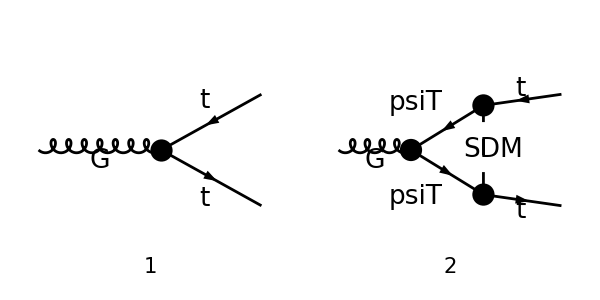

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  {V[4]}->  {-F[9],F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]
```

in total: 2 Particles amplitudes

ⅈ gs T_c2c1^cc3 ((ⅈ yDM^2 (γ̄)^7.(mPsiT-γ·(p1+p2+q)).γ^μ.(mPsiT-γ·q).(γ̄)^6)/((q^2-mPsiT^2).((p1+q)^2-mSDM^2).((p1+p2+q)^2-mPsiT^2))+(2 π^2 deltaCTL yDM^2+1) γ^μ.(γ̄)^7+(2 π^2 deltaCTR yDM^2+1) γ^μ.(γ̄)^6)

```mathematica
ampSM1=gs SeriesCoefficient[ampB,{gs,0,1},{yDM,0,0}]
FullSimplify[ampB - ampSM1]
```

ⅈ gs (γ^μ.(γ̄)^6+γ^μ.(γ̄)^7) T_c2c1^cc3

ⅈ gs yDM^2 T_c2c1^cc3 (2 π^2 (deltaCTL γ^μ.(γ̄)^7+deltaCTR γ^μ.(γ̄)^6)+(ⅈ (γ̄)^7.(mPsiT-γ·(p1+p2+q)).γ^μ.(mPsiT-γ·q).(γ̄)^6)/((q^2-mPsiT^2).((p1+q)^2-mSDM^2).((p1+p2+q)^2-mPsiT^2)))

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}]
```

ⅈ gs T_c2c1^cc3 (π^2 yDM^2 γ^μ.(γ̄)^6 B_0(MT^2,mPsiT^2,mSDM^2)+π^2 yDM^2 ((γ·p1).γ^μ.(γ·p1).(γ̄)^6-2 p1^μ (γ·p1).(γ̄)^6+(γ·p2).γ^μ.(γ·p1).(γ̄)^6) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)-2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+π^2 yDM^2 (-2 p1^μ (γ·p1).(γ̄)^6+(γ·p1).γ^μ.(γ·(p1-p2)).(γ̄)^6+(γ·p2).γ^μ.(γ·(p1-p2)).(γ̄)^6-2 p1^μ (γ·(p1-p2)).(γ̄)^6+2 p2^μ (γ·p1).(γ̄)^6) C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)-2 π^2 yDM^2 (p1^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6) C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+γ^μ.((γ̄)^6+(γ̄)^7)+2 π^2 deltaCTL yDM^2 γ^μ.(γ̄)^7+2 π^2 deltaCTR yDM^2 γ^μ.(γ̄)^6)

```mathematica
(* Remove SM contribution *)
ampSM=gs SeriesCoefficient[ampC,{gs,0,1},{yDM,0,0}]
ampC=Simplify[DiracSimplify[ampC-ampSM]]
```

ⅈ gs T_c2c1^cc3 (φ(-p2,MT)).(γ·ε(p3)).((γ̄)^6+(γ̄)^7).(φ(p1,MT))

ⅈ π^2 gs yDM^2 T_c2c1^cc3 ((B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+MT^2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+deltaCTR)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+(MT^2 (-C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2))-2 MT^2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+2 deltaCTL) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^7.(φ(p1,MT))+2 MT (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) ((p2·ε(p3)) (C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))-(p1·ε(p3)) C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))-2 MT (φ(-p2,MT)).(γ̄)^7.(φ(p1,MT)) ((p1·ε(p3)) (C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))-(p2·ε(p3)) C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)))

## Off - Shell Case

```mathematica
FCClearScalarProducts[];
```

```mathematica
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
```

```mathematica
ampD=FullSimplify[FCReplaceMomenta[ampC,{p3->-p1-p2}]];
```

```mathematica
ampEsimp2=FullSimplify[ExpandScalarProduct[ampD/.{DiracGamma[7]->1-DiracGamma[6]}]]
```

ⅈ π^2 gs yDM^2 T_c2c1^cc3 ((B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+MT^2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+deltaCTR)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+(2 deltaCTL-MT^2 (C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))) (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))-2 MT (C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)) ((p1·ε(p3)) (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT))-(p2·ε(p3)) (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)))+2 MT C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) ((p2·ε(p3)) (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT))-(p1·ε(p3)) (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT))))

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(B_0(p2^2,mPsiT^2,mSDM^2) | 1/ε_UV
C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2) | 0
C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_00(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 1/(4 ε_UV)
C_11(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_11(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2) | 0
C_12(p1^2,s,p2^2,mSDM^2,mPsiT^2,mPsiT^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
(* Divergences from counter-terms *)
Coefficient[ampEsimp2,deltaCTR];
ctUV=FullSimplify[SUNSimplify[Coefficient[ampEsimp2,deltaCTR] ] (-1/(64 π^4 EpsilonUV)) ] ;
FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[loopUV+ctUV,DiracSubstitute67->False]]]
```

0

## Coefficients for Loop Amplitude

```mathematica
args1={Pair[Momentum[p1,D],Momentum[p1,D]],s,Pair[Momentum[p2,D],Momentum[p2,D]]};
args2={mSDM^2,mPsiT^2,mPsiT^2};
argsNew={p1sq,s,p2sq};
subs2={PaVe[0,0,args1,args2,a___]->C00eff@@argsNew+deltaCTL-deltaCTR,PaVe[1,1,args1,args2,a___]->C11@@argsNew,PaVe[2,2,args1,args2,a___]->C22@@argsNew,PaVe[1,2,args1,args2,a___]->C12@@argsNew,PaVe[1,args1,args2,a___]->C1@@argsNew,PaVe[2,args1,args2,a___]->C2@@argsNew};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
pairs1=Cases2[ampEsimp3,Pair];
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{(γ̄)^6,γ^μ,γ·p1,γ·p2,γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p1).γ^μ.(γ·p2).(γ̄)^6,(γ·p2).γ^μ.(γ·p1).(γ̄)^6}

{p1^μ,p2^μ,p1^2,p2^2,p1^μ p2^μ,p1^2 p1^μ,p2^2 p1^μ,p1^2 p2^μ,p2^2 p2^μ,p1^2 p2^2}

{T_c2c1^cc3}

### Coefficients for each term

Define short names for each coefficient

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

We have to deal with the terms without explicit momenta separately:

```mathematica
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3/.{Pair[LorentzIndex[μ,D],Momentum[p2,D]]->0,Pair[LorentzIndex[μ,D],Momentum[p1,D]]->0}],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],1,c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs yDM^2  Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

-ⅈ π^2 gs yDM^2 γ^μ.(γ̄)^6 T_c2c1^cc3 (p1^2 C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+p1^2 C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)-p2^2 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))

```mathematica
su3Terms (*VLF*)
```

(T_c2c1^cc3 | γ^μ.(γ̄)^6 | p1^2 | -C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)-C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | γ^μ.(γ̄)^6 | p2^2 | C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p1^μ | -2 (C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+C_11(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))
T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p2^μ | 2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C12(p1sq,s,p2sq))
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p1^μ | 2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C12(p1sq,s,p2sq))
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p2^μ | -2 (C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)+C_11(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2))
T_c2c1^cc3 | γ^μ | 1 | 2 deltaCTL
T_c2c1^cc3 | γ^μ.(γ̄)^6 | 1 | -p1^2 (C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))+B_0(p2^2,mPsiT^2,mSDM^2)-2 (C_00(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2)+deltaCTL-deltaCTR)+p2^2 C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p1).γ^μ.(γ·p2).(γ̄)^6 | 1 | -C_1(s,p2^2,p1^2,mPsiT^2,mPsiT^2,mSDM^2)
T_c2c1^cc3 | (γ·p2).γ^μ.(γ·p1).(γ̄)^6 | 1 | C_0(p1^2,p2^2,s,mPsiT^2,mSDM^2,mPsiT^2)+C_1(s,p1^2,p2^2,mPsiT^2,mPsiT^2,mSDM^2))

## On - Shell Regime and Degenerate

```mathematica
SPD[p1,p1]=MT^2;
SPD[p2,p2]=MT^2;
```

```mathematica
SubsCT={deltaCTL-> -1/(128 Subscript[g, s] √lA π^6 xT^2 Subscript[y, DM]^2)ⅈ (√lA xT (2-2 xC+xT)+√lA (1+xC^2-xC (2+xT)) Log[xC]+((-1+xC)^3+(1+xC-2 xC^2) xT+xC xT^2) (Log[4]+Log[xC]-2 Log[1+xC-xT+√((-1+xC)^2-2 (1+xC) xT+xT^2)])),deltaCTR-> 1/(128 √lA π^4 xT^2)(√lA ((-1+xC)^2+xT^2) Log[xC]-2 (-1+xC+xT) (√lA xT+(1+xC^2+xT^2-2 xC (1+xT)) Log[(1+√lA+xC-xT)/(2 √xC)])),xC-> 1,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
deltaCTLDG= Limit[Limit[deltaCTL/.SubsCT/.lA-> xC^2+(1-xT)^2-2*xC*(1+xT),xC->1],xT->0]
deltaCTRDG = Limit[Limit[deltaCTR/.SubsCT/.lA-> xC^2+(1-xT)^2-2*xC*(1+xT),xC->1],xT->0]
```

0

0

```mathematica
ampEsimp2 = Expand[Collect[Simplify[(  ampEsimp2)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
ampEsimpOnShell = FullSimplify[ampEsimp2]
```

ⅈ π^2 gs yDM^2 T_c2c1^cc3 ((B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-mPsiT^2) C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 (-C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+MT^2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+deltaCTR)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+(2 deltaCTL-MT^2 (C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2)+2 C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2))) (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))-2 MT (C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)+C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)) ((p1·ε(p3)) (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT))-(p2·ε(p3)) (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)))+2 MT C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2) ((p2·ε(p3)) (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT))-(p1·ε(p3)) (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT))))

The raw FeynCalc output is mathematically equivalent to the final analytical expression presented in the text. However, because FeynCalc automatically evaluates the amplitude in the fully symmetric on-shell limit (p1^2 = p2^2 = MT^2), recovering the exact bracketed structure requires applying four specific kinematic and algebraic relations:

1. Passarino-Veltman Kinematic Symmetries
Because the incoming and outgoing top quarks are on-shell and share the exact same mass, the loop integrals are fully symmetric under the exchange of p1 and p2. Applying this symmetry yields:

C2 -> C1

C22 -> C11

This explains why the raw output groups the three-matrix chain into (C0 + 2C1) rather than (C0 + C1 + C2), and why C11 appears factored with both p1^[Mu] and p2^[Mu] instead of mixing with C22.

2. The Dirac Reversal Identity
To group the unsimplified chain -(p1_slash) [Gamma]^[Mu] (p2_slash) Overscript[[Gamma], _]^6 C1 into the (p2_slash) [Gamma]^[Mu] (p1_slash) and individual vector terms seen in the analytical expression, we apply the standard Dirac reversal identity:

(p1_slash) [Gamma]^[Mu] (p2_slash) = (p2_slash) [Gamma]^[Mu] (p1_slash) - 2 p1^[Mu] (p2_slash) - 2 p2^[Mu] (p1_slash) + 2(p1.p2) [Gamma]^[Mu]

When substituted, the -2 p1^[Mu] (p2_slash) and -2 p2^[Mu] (p1_slash) terms perfectly cancel the stray C1 coefficients mixed inside the C12 brackets, leaving exactly -2 p2^[Mu] C12 and -2 p1^[Mu] C12.

3. Mandelstam Expansion

The reversal identity generates a residual +2(p1.p2) [Gamma]^[Mu] P_R C1 term. By applying the on-shell Mandelstam relation:

2(p1.p2) = s - 2 MT^2

this residual expands into s [Gamma]^[Mu] P_R C1 - 2 MT^2 [Gamma]^[Mu] P_R C1. When grouped with the existing [Gamma]^[Mu] P_R terms, it yields the exact +4 MT^2 C1 coefficient present in the final expression (which was originally written as 2 p1^2 C1 + 2 p2^2 C2).

4. Chiral Projector Collapse
The raw output ends with + 2 [Delta]CTL [Gamma]^[Mu] (1 - Overscript[[Gamma], _]^6). Substituting the right-handed projector (Overscript[[Gamma], _]^6 = P_R) collapses the term directly into the left-handed state:

[Gamma]^[Mu] (1 - P_R) = [Gamma]^[Mu] P_L

yielding exactly + 2 [Delta]L [Gamma]^[Mu] P_L.

```mathematica
loopFuncs = Cases[ampEsimpOnShell, _B0 | _C0 | _PaVe, Infinity] // DeleteDuplicates;
pos=Flatten[Position[loopFuncs,_B0]];
loopFuncs[[pos]] = loopFuncs[[pos]]/.{MT^2->s};
loopFuncs
```

{C_0(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2),C_1(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2),B_0(s,mPsiT^2,mPsiT^2),C_00(MT^2,MT^2,s,mPsiT^2,mSDM^2,mPsiT^2),C_11(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2),C_12(MT^2,s,MT^2,mSDM^2,mPsiT^2,mPsiT^2)}

```mathematica
loopFuncsEFT1=Table[FullSimplify[PaXEvaluate[loopFuncs[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{mSDM,mPsiT,0}}]/.{EulerGamma->0,ScaleMu->mPsiT/(√(4 Pi))}],{i,1,Length[loopFuncs]}]
loopFuncs[[pos]] = loopFuncs[[pos]]/.{s->MT^2};
```

{(log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)))/(32 π^4 s),(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)/(16 π^4 s^2),(ε √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 ε s+s)/(16 π^4 ε s),(ε log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)) (√(s (s-4 mPsiT^2))+mPsiT^2 log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2)))+3 ε s+s)/(64 π^4 ε s),-(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s)/(32 π^4 s^2),(mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+s)/(32 π^4 s^2)}

```mathematica
loopSubs = Table[loopFuncs[[i]]-> loopFuncsEFT1[[i]],{i,1,Length[loopFuncs]}];
```

```mathematica
ampEFT1 =Collect[Simplify[ ampEsimpOnShell/.loopSubs/.{deltaCTL->0,deltaCTR->0}],{Epsilon,s,mPsiT,Log[a_],deltaCTL,deltaCTR},Simplify]
```

(ⅈ gs (32 π^4 B_0(s,mPsiT^2,mPsiT^2)-3) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT)) T_c2c1^cc3 yDM^2)/(32 π^2)-(ⅈ gs (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT)) T_c2c1^cc3 yDM^2)/(32 ε π^2)+1/s(-(ⅈ gs mPsiT^2 (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT)) log^2((2 mPsiT^2-s+√(s (s-4 mPsiT^2)))/(2 mPsiT^2)) T_c2c1^cc3 yDM^2)/(16 π^2)-1/(32 π^2)ⅈ gs (MT^2 (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))-mSDM^2 (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))) log^2((2 mPsiT^2-s+√(s (s-4 mPsiT^2)))/(2 mPsiT^2)) T_c2c1^cc3 yDM^2-(ⅈ gs √(s (s-4 mPsiT^2)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT)) log((2 mPsiT^2-s+√(s (s-4 mPsiT^2)))/(2 mPsiT^2)) T_c2c1^cc3 yDM^2)/(32 π^2)-1/(16 π^2)ⅈ gs MT (4 MT (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))-4 MT (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+2 (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT)) (p1·ε(p3))+(φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) (p1·ε(p3))-(φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT)) (p2·ε(p3))-2 (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) (p2·ε(p3))) T_c2c1^cc3 yDM^2)+1/s^2(-1/(16 π^2)ⅈ gs mPsiT^2 MT log^2((2 mPsiT^2-s+√(s (s-4 mPsiT^2)))/(2 mPsiT^2)) ((φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) (p1·ε(p3))-(φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT)) (p2·ε(p3))) T_c2c1^cc3 yDM^2-1/(16 π^2)ⅈ gs MT √(s (s-4 mPsiT^2)) log((2 mPsiT^2-s+√(s (s-4 mPsiT^2)))/(2 mPsiT^2)) (2 MT (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))-2 MT (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+(φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT)) (p1·ε(p3))-(φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) (p2·ε(p3))) T_c2c1^cc3 yDM^2)

```mathematica
ampEFT1b=Simplify[ampEFT1]
```

-1/(32 π^2 ε s^2)ⅈ gs yDM^2 T_c2c1^cc3 ((-32 π^4 ε s^2 B_0(s,mPsiT^2,mPsiT^2)+ε s (2 mPsiT^2-mSDM^2) log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+ε √(s (s-4 mPsiT^2)) (s-4 MT^2) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+s (-8 ε MT^2+3 ε s+s)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+ε MT^2 (s log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+4 √(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+8 s) (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT))+2 ε MT (((mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+s) (p1·ε(p3))-(√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s) (p2·ε(p3))) (φ(-p2,MT)).(γ̄)^6.(φ(p1,MT))+((√(s (s-4 mPsiT^2)) log((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+2 s) (p1·ε(p3))-(mPsiT^2 log^2((√(s (s-4 mPsiT^2))+2 mPsiT^2-s)/(2 mPsiT^2))+s) (p2·ε(p3))) (φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT))))

```mathematica
ampEFT1c = Collect[ampEFT1b/.{Log[(√(s(s-4 mPsiT^2))+2 mPsiT^2 -s)/(2 mPsiT^2)]->L[s,mPsiT],√(s(s-4 mPsiT^2))->Δ[s,mPsiT]},{Epsilon},FullSimplify]
```

-1/(32 π^2 s^2)ⅈ gs yDM^2 T_c2c1^cc3 (((s-4 MT^2) L(s,mPsiT) Δ(s,mPsiT)-s (32 π^4 s B_0(s,mPsiT^2,mPsiT^2)+(mSDM^2-2 mPsiT^2) (L(s,mPsiT))^2+8 MT^2-3 s)) (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT))+2 MT ((φ(-p2,MT)).(1-(γ̄)^6).(φ(p1,MT)) ((p1·ε(p3)) (L(s,mPsiT) Δ(s,mPsiT)+2 s)-(mPsiT^2 (L(s,mPsiT))^2+s) (p2·ε(p3)))+(φ(-p2,MT)).(γ̄)^6.(φ(p1,MT)) ((mPsiT^2 (L(s,mPsiT))^2+s) (p1·ε(p3))-(p2·ε(p3)) (L(s,mPsiT) Δ(s,mPsiT)+2 s)))+MT^2 (4 L(s,mPsiT) Δ(s,mPsiT)+s ((L(s,mPsiT))^2+8)) (φ(-p2,MT)).(γ·ε(p3)).(1-(γ̄)^6).(φ(p1,MT)))-(ⅈ gs yDM^2 T_c2c1^cc3 (φ(-p2,MT)).(γ·ε(p3)).(γ̄)^6.(φ(p1,MT)))/(32 π^2 ε)

## Get Counter Term Expressions for LATEX:

```mathematica
deltaCTLexp=FullSimplify[(deltaCTL/.SubsCT)/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

-1/(128 π^6 √λ y_DM^2 g_s x_t^2)ⅈ ((x_t (x x_t-2 x^2+x+1)+(x-1)^3) (-2 log(-x_t+√(x_t^2-2 (x+1) x_t+(x-1)^2)+x+1)+log(x)+log(4))+√λ x_t (x_t-2 x+2)+√λ ((x-1)^2-x x_t) log(x))

```mathematica
TeXForm[deltaCTLexp]
```

-\frac{i \left(\left(x_t \left(x x_t-2 x^2+x+1\right)+(x-1)^3\right) \left(-2 \log
   \left(-x_t+\sqrt{x_t^2-2 (x+1) x_t+(x-1)^2}+x+1\right)+\log (x)+\log
   (4)\right)+\sqrt{\lambda } x_t \left(x_t-2 x+2\right)+\sqrt{\lambda }
   \left((x-1)^2-x x_t\right) \log (x)\right)}{128 \pi ^6 \sqrt{\lambda }
   y_{\text{DM}}^2 g_s x_t^2}

```mathematica
deltaCTRexp=FullSimplify[deltaCTR/.SubsCT/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

(√λ (x_t^2+(x-1)^2) log(x)-2 (x_t+x-1) (√λ x_t+(x_t^2-2 x x_t+(x-1)^2) log((√λ-x_t+x+1)/(2 √x))))/(128 π^4 √λ x_t^2)

```mathematica
TeXForm[deltaCTRexp]
```

\frac{\left(-x_t+x-1\right) \left(2 \left(\left(x_t-1\right){}^2+(x-2) x\right) \log \left(\frac{\sqrt{\lambda
   }-x_t+x+1}{2 \sqrt{x}}\right)+\sqrt{\lambda } \left(2 x_t-\left(x_t+x-1\right) \log (x)\right)\right)}{128 \pi
   ^4 \sqrt{\lambda } x_t^2}

```mathematica
lAexp = (1-2*xC+xC^2-2*xT-2*xC*xT+xT^2)/.{xC->x,xT-> Subscript[x, t],lA-> λ}
```

-2 x x_t+x_t^2-2 x_t+x^2-2 x+1

```mathematica
TeXForm[lAexp]
```

-2 x x_t+x_t^2-2 x_t+x^2-2 x+1